```mathematica
N[(π)^(ⅇ) - Exp[π]]
```

-0.681535

```mathematica
-----------2st task-------
```

```mathematica
N[(2)^(1/2)-Log[3],30]
```

0.315601273704985357406443487287

```mathematica
-----------3st task-------
```

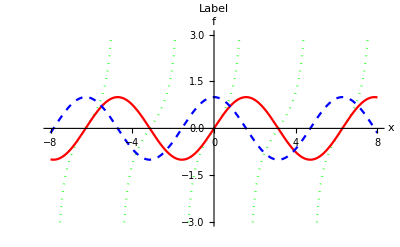

```mathematica
Plot[{Tan[x],Sin[x],Cos[x]},{x,-8,8},PlotLabel->"Label",AxesLabel->{x,f},PlotStyle->{Directive[Dotted,Green],Red,Directive[Dashed,Blue]},PlotRange->{{-8,8},{-3,3}}]
```

```mathematica
-----------4st task-------
```

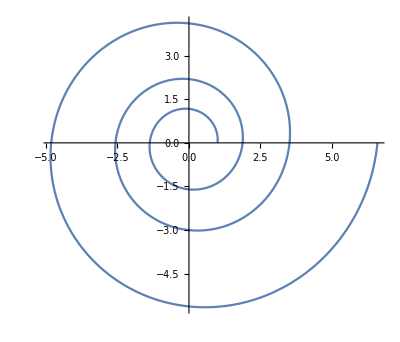

```mathematica
PolarPlot[Exp[1/10*ϕ],{ϕ,0,6*π}]
```

```mathematica
ParametricPlot[{Exp[1/10*ϕ]*Cos[ϕ],Exp[1/10*ϕ]*Sin[ϕ]},{ϕ,0,6*π}]
```

-Graphics-

```mathematica
-----------5st task-------
```

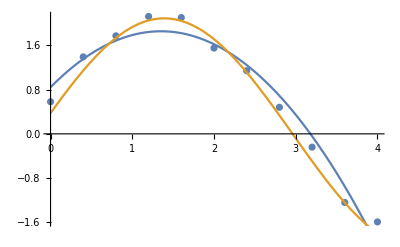

```mathematica
data={{0., 0.58}, {0.4, 1.39}, {0.8, 1.77}, {1.2, 2.12}, {1.6, 2.10},{2.,1.55}, {2.4, 1.14}, {2.8,0.48}, {3.2,-0.24}, {3.6,-1.24}, {4.,-1.59}};
f1 = Fit[data,{1,x,x^2},{x}];
f2 = Fit[data,{Sin[x],Cos[x]},x];
Show[ListPlot[data],Plot[{f1,f2},{x,0,4}]]
```

```mathematica
-----------6st task-------
```

```mathematica
Plot3D[Sin[Sqrt[x^2+y^2]]/(Sqrt[x^2+y^2]),{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
-----------7st task-------
```

```mathematica
ParametricPlot3D[{(10+3Cos[θ])Cos[ϕ],(10+3Cos[θ])Sin[ϕ],3Sin[θ]},{ϕ,0,2π},{θ,-π,π}]
```

-Graphics3D-

```mathematica
-----------8st task-------
```

```mathematica
Normal[Series[BesselJ[n+1/2,x],{x,0,3}]]
Normal[Series[BesselJ[n+1/2,x],{x,∞,1}]]
```

x^n ((2^(-1/2-n) √x)/Gamma[3/2+n]-(2^(-5/2-n) x^(5/2))/((3/2+n) Gamma[3/2+n]))

(√(2/π) Cos[1/2 (π+n π)-x])/(√x)+((n+n^2) Sin[1/2 (π+n π)-x])/(√(2 π) x^(3/2))

```mathematica
-----------9st task-------
```

```mathematica
A = Cancel[Sqrt[1/Integrate[(r^2)Exp[-2r/a],{r,0,∞},Assumptions->a>0]/(4π)]]
Solve[(B^2)4π Integrate[(r^2)Exp[-2r/a],{r,0,∞},Assumptions->a>0]==1,B]
```

(√(1/a^3))/(√π)

{{B→-1/(a^(3/2) √π)},{B→1/(a^(3/2) √π)}}